## Project 1 data plot.

### Wah Loon Keng.

```mathematica
Today
```

Fri 21 Nov 2014

### Import Data

```mathematica
Subscript[data, 1]=Transpose[Import["~/Google Drive/Courses/CS 150/P3/P3 report/timing.txt","Data"]];
```

```mathematica
Subscript[data, 2]=Transpose[Import["~/Google Drive/Courses/CS 150/P3/analysis.txt","Data"]];
```

```mathematica
Subscript[dat, x_]:=Transpose[{Subscript[data, x]⟦1⟧,Subscript[data, x]⟦2⟧}];
Subscript[dat, x_,y_]:=Transpose[{Subscript[data, x]⟦1⟧,Subscript[data, x]⟦y+1⟧}];
```

```mathematica
Subscript[dat, 1];
```

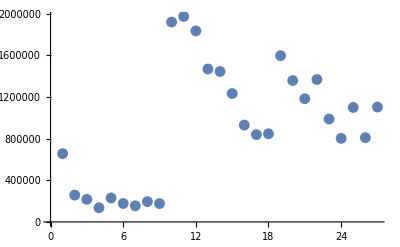

```mathematica
ListPlot[Subscript[dat, 1]]
```

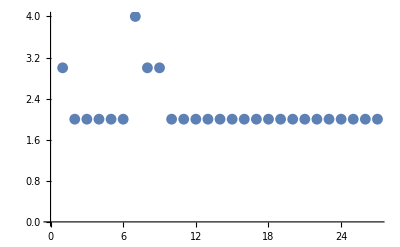

```mathematica
ListPlot[Subscript[dat, 2,1]]
```

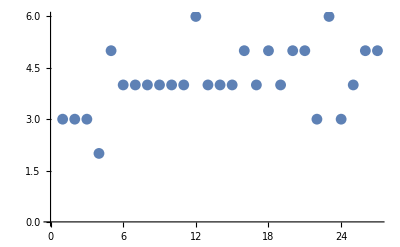

```mathematica
ListPlot[Subscript[dat, 2,2]]
```

### Draw function

```mathematica
dataList={Subscript[dat, 2,1],Subscript[dat, 2,2],Subscript[dat, 2,3],Subscript[dat, 2,4],Subscript[dat, 2,5],Subscript[dat, 2,6]};
legendList={
""
};
labelList={"NNGraph v.s. dataset index"};
varList={
"dataset","minSize","maxSize","avgSize","minDist","maxDist","avgDist"
};
```

```mathematica
(*Draw[whichdata_]:=(
ListPlot[dataList⟦whichdata⟧,PlotMarkers->Automatic, PlotLegends->legendList⟦whichdata⟧,AxesLabel->{"tree size","time (ns)"},ImageSize->500, PlotLabel->labelList⟦whichdata⟧]
)*)
```

```mathematica
Draw[x__,legends__,plotlabel_,varN_]:=(
ListPlot[dataList⟦x⟧,PlotMarkers->Automatic,PlotRange->All, PlotLegends->{legendList⟦legends⟧},AxesLabel->{varList⟦1⟧,varList⟦varN+1⟧},ImageSize->500, PlotLabel->labelList⟦plotlabel⟧]
)
```

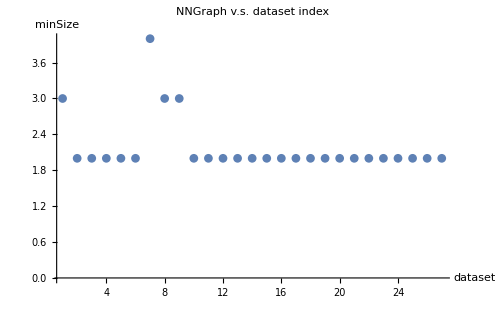

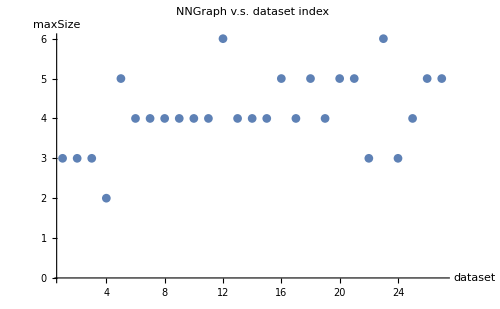

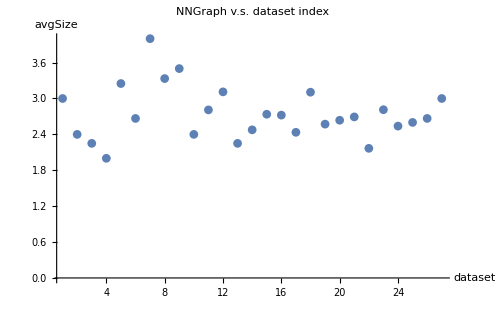

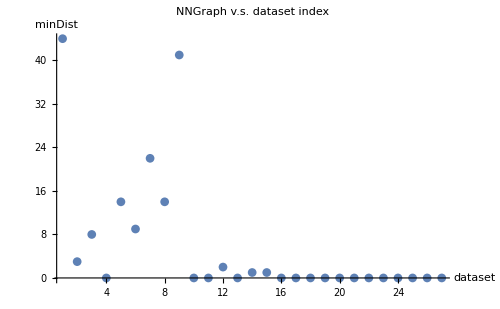

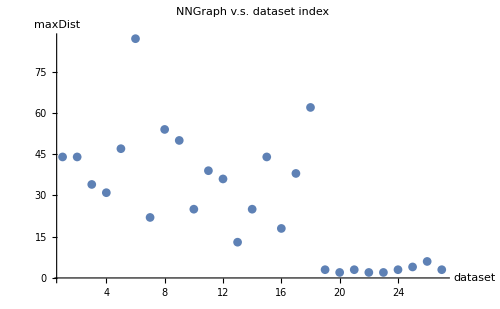

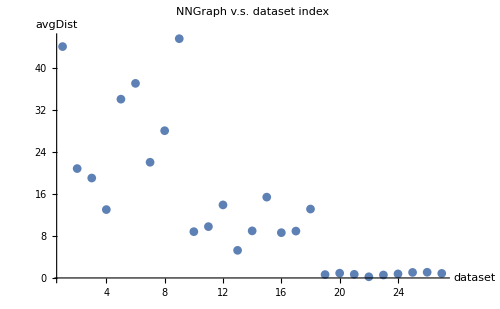

```mathematica
For[i=1,i<7,i++,
Print[Draw[{i},{},1,i]]
]
```

## Fit

```mathematica
show[fitted_,data_,legend_,plotlabel_]:=(
Show[ListPlot[data,PlotLegends->{legend},AxesLabel->{"vertices","Search time(ns)"}],Plot[fitted[x],{x,0,10000}],ImageSize->500, PlotLabel->labelList⟦plotlabel⟧]
)
```

```mathematica
show2[fitted_,data_,legend_,plotlabel_]:=(
Show[ListPlot[data,PlotLegends->{legend},AxesLabel->{"edges","Search time(ns)"}],Plot[fitted[x],{x,0,10000}],ImageSize->500, PlotLabel->labelList⟦plotlabel⟧]
)
```

```mathematica
showFitted[x1_,x2_,fit_,legends_,plotlabel_]:=(
Print[fit[dataList⟦x1⟧]];
Print[fit[dataList⟦x2⟧]];
Show[
ListPlot[dataList⟦{x1,x2}⟧,PlotLegends->{legendList⟦legends⟧},AxesLabel->{"tree size","time (ns)"},PlotLabel->labelList⟦plotlabel⟧],
Plot[{fit[dataList⟦x1⟧][y],fit[dataList⟦x2⟧][y]},{y,0,10000}],ImageSize->500]
)
```

```mathematica
(*showFitted[1,4,fitN1,{1,2},1]*)
```

```mathematica
fitN1[data_]:=(
NonlinearModelFit[data,a x,{a},x]
)
fitN2[data_]:=(
NonlinearModelFit[data,{a x Log[b x],0.2>b>0},{a,b},x]
)
```

FittedModel[330270. x Log[0.0909059 x]]

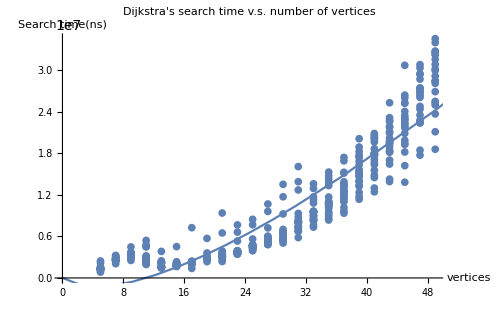

```mathematica
i=1;
aMax=10;
fitN2[dataList⟦i⟧]
show[%,dataList⟦i⟧,{},1]
```

FittedModel[15974.4 x]

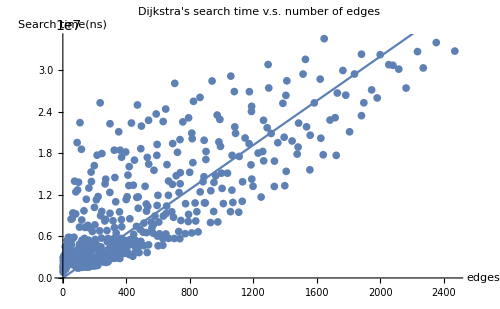

```mathematica
i=2;
aMax=10;
fitN1[dataList⟦i⟧]
show2[%,dataList⟦i⟧,{},2]
```

```mathematica
fitN3[data_]:=(
NonlinearModelFit[data,{a y + c x Log[b x],1>b>0},{a,b,c},{y,x}]
)
i=3;
tmp=fitN3[dataList⟦i⟧]

Show[
Plot3D[tmp[x,y],{x,0,50},{y,0,2500},PlotStyle->Opacity[0.1],
RegionFunction->Function[{x,y,z},y-x^2<0],
AxesLabel->{"vertices","edges","Search time(ns)"}
],
ListPointPlot3D[Subscript[dat3, 1]],
ImageSize->600]
(*show[%,dataList⟦i⟧,legendList⟦i⟧]*)
```

FittedModel[255374. y+1089.34 x Log[0.454538 x]]

-Graphics3D-